```mathematica
Table[{
Last[ComposeList[(Rest[IntegerDigits[k+2,2]]/.{0->"Even",1->"Odd"}),x]],
(IntegerToList[k]//Factor//TraditionalForm)
}
,{k,0,20}]//TableForm
```

Even[x] | x/2
Odd[x] | 3 x+1
Even[Even[x]] | x/4
Odd[Even[x]] | 1/2 (3 x+1)
Even[Odd[x]] | 1/2 (3 x+2)
Odd[Odd[x]] | 9 x+4
Even[Even[Even[x]]] | x/8
Odd[Even[Even[x]]] | 1/4 (3 x+1)
Even[Odd[Even[x]]] | 1/4 (3 x+2)
Odd[Odd[Even[x]]] | 1/2 (9 x+4)
Even[Even[Odd[x]]] | 1/4 (3 x+4)
Odd[Even[Odd[x]]] | 1/2 (9 x+5)
Even[Odd[Odd[x]]] | 1/2 (9 x+8)
Odd[Odd[Odd[x]]] | 27 x+13
Even[Even[Even[Even[x]]]] | x/16
Odd[Even[Even[Even[x]]]] | 1/8 (3 x+1)
Even[Odd[Even[Even[x]]]] | 1/8 (3 x+2)
Odd[Odd[Even[Even[x]]]] | 1/4 (9 x+4)
Even[Even[Odd[Even[x]]]] | 1/8 (3 x+4)
Odd[Even[Odd[Even[x]]]] | 1/4 (9 x+5)
Even[Odd[Odd[Even[x]]]] | 1/4 (9 x+8)

```mathematica
Table[{
Last[ComposeList[(Rest[IntegerDigits[k+2,2]]/.{0->"Even",1->"Odd"}),x]],
(IntegerToList[k]==x//Simplify//TraditionalForm),
(First[First[Solve[IntegerToList[k]==x,x]]])
}
,{k,0,20}]//TableForm
```

Even[x] | x==0 | x→0
Odd[x] | 2 x+1==0 | x→-1/2
Even[Even[x]] | x==0 | x→0
Odd[Even[x]] | x+1==0 | x→-1
Even[Odd[x]] | x+2==0 | x→-2
Odd[Odd[x]] | 2 x+1==0 | x→-1/2
Even[Even[Even[x]]] | x==0 | x→0
Odd[Even[Even[x]]] | x==1 | x→1
Even[Odd[Even[x]]] | x==2 | x→2
Odd[Odd[Even[x]]] | 7 x+4==0 | x→-4/7
Even[Even[Odd[x]]] | x==4 | x→4
Odd[Even[Odd[x]]] | 7 x+5==0 | x→-5/7
Even[Odd[Odd[x]]] | 7 x+8==0 | x→-8/7
Odd[Odd[Odd[x]]] | 2 x+1==0 | x→-1/2
Even[Even[Even[Even[x]]]] | x==0 | x→0
Odd[Even[Even[Even[x]]]] | 5 x==1 | x→1/5
Even[Odd[Even[Even[x]]]] | 5 x==2 | x→2/5
Odd[Odd[Even[Even[x]]]] | 5 x+4==0 | x→-4/5
Even[Even[Odd[Even[x]]]] | 5 x==4 | x→4/5
Odd[Even[Odd[Even[x]]]] | x+1==0 | x→-1
Even[Odd[Odd[Even[x]]]] | 5 x+8==0 | x→-8/5

```mathematica
Table[{
Last[ComposeList[(Rest[IntegerDigits[k+2,2]]/.{0->"Even",1->"Odd"}),x]],
(IntegerToListSym[k]==x//Factor//TraditionalForm),
(First[First[Solve[IntegerToListSym[k]==x,x]]])
}
,{k,0,20}]//TableForm
```

Even[x] | x/2==x | x→0
Odd[x] | 3 x+1==x | x→-1/(-1+3)
Even[Even[x]] | x/2^2==x | x→0
Odd[Even[x]] | (3 x+1)/2==x | x→1/(2-3)
Even[Odd[x]] | (3 x+1 2)/2==x | x→(1 2)/(2-3)
Odd[Odd[x]] | 3^2 x+1 3+1==x | x→-1/(-1+3)
Even[Even[Even[x]]] | x/2^3==x | x→0
Odd[Even[Even[x]]] | (3 x+1)/2^2==x | x→1/(2^2-3)
Even[Odd[Even[x]]] | (3 x+1 2)/2^2==x | x→(1 2)/(2^2-3)
Odd[Odd[Even[x]]] | (3^2 x+1 3+1)/2==x | x→(1+1 3)/(2-3^2)
Even[Even[Odd[x]]] | (3 x+1 2^2)/2^2==x | x→-(1 2^2)/(-2^2+3)
Odd[Even[Odd[x]]] | (3^2 x+1 3+1 2)/2==x | x→(1 (2+3))/(2-3^2)
Even[Odd[Odd[x]]] | (3^2 x+1 2 3+1 2)/2==x | x→-(2 (1+1 3))/(-2+3^2)
Odd[Odd[Odd[x]]] | 3^3 x+1 3^2+1 3+1==x | x→-1/(-1+3)
Even[Even[Even[Even[x]]]] | x/2^4==x | x→0
Odd[Even[Even[Even[x]]]] | (3 x+1)/2^3==x | x→1/(2^3-3)
Even[Odd[Even[Even[x]]]] | (3 x+1 2)/2^3==x | x→(1 2)/(2^3-3)
Odd[Odd[Even[Even[x]]]] | (3^2 x+1 3+1)/2^2==x | x→(1+1 3)/(2^2-3^2)
Even[Even[Odd[Even[x]]]] | (3 x+1 2^2)/2^3==x | x→(1 2^2)/(2^3-3)
Odd[Even[Odd[Even[x]]]] | (3^2 x+1 3+1 2)/2^2==x | x→1/(2-3)
Even[Odd[Odd[Even[x]]]] | (3^2 x+1 2 3+1 2)/2^2==x | x→(2 (1+1 3))/(2^2-3^2)

```mathematica
Table[{
Last[ComposeList[(Rest[IntegerDigits[k+2,2]]/.{0->"Even",1->"Odd"}),x]],
Solve[IntegerToList[k]==x,x],
(IntegerToList[k]==x//Factor//TraditionalForm),
(IntegerToListSym[k]==x//Factor//TraditionalForm),
(IntegerToListSym[k]==x//Factor//TraditionalForm),
(First[First[Solve[IntegerToListSym[k]==x,x]]])
}
,{k,0,80}]//TableForm
```

Even[x] | x→0 | x/2==x | x/2==x | x/2==x | x→0
Odd[x] | x→-1/2 | 3 x+1==x | 3 x+1==x | 3 x+1==x | x→-1/(-1+3)
Even[Even[x]] | x→0 | x/4==x | x/2^2==x | x/2^2==x | x→0
Odd[Even[x]] | x→-1 | 1/2 (3 x+1)==x | (3 x+1)/2==x | (3 x+1)/2==x | x→1/(2-3)
Even[Odd[x]] | x→-2 | 1/2 (3 x+2)==x | (3 x+1 2)/2==x | (3 x+1 2)/2==x | x→(1 2)/(2-3)
Odd[Odd[x]] | x→-1/2 | 9 x+4==x | 3^2 x+1 3+1==x | 3^2 x+1 3+1==x | x→-1/(-1+3)
Even[Even[Even[x]]] | x→0 | x/8==x | x/2^3==x | x/2^3==x | x→0
Odd[Even[Even[x]]] | x→1 | 1/4 (3 x+1)==x | (3 x+1)/2^2==x | (3 x+1)/2^2==x | x→1/(2^2-3)
Even[Odd[Even[x]]] | x→2 | 1/4 (3 x+2)==x | (3 x+1 2)/2^2==x | (3 x+1 2)/2^2==x | x→(1 2)/(2^2-3)
Odd[Odd[Even[x]]] | x→-4/7 | 1/2 (9 x+4)==x | (3^2 x+1 3+1)/2==x | (3^2 x+1 3+1)/2==x | x→(1+1 3)/(2-3^2)
Even[Even[Odd[x]]] | x→4 | 1/4 (3 x+4)==x | (3 x+1 2^2)/2^2==x | (3 x+1 2^2)/2^2==x | x→-(1 2^2)/(-2^2+3)
Odd[Even[Odd[x]]] | x→-5/7 | 1/2 (9 x+5)==x | (3^2 x+1 3+1 2)/2==x | (3^2 x+1 3+1 2)/2==x | x→(1 (2+3))/(2-3^2)
Even[Odd[Odd[x]]] | x→-8/7 | 1/2 (9 x+8)==x | (3^2 x+1 2 3+1 2)/2==x | (3^2 x+1 2 3+1 2)/2==x | x→-(2 (1+1 3))/(-2+3^2)
Odd[Odd[Odd[x]]] | x→-1/2 | 27 x+13==x | 3^3 x+1 3^2+1 3+1==x | 3^3 x+1 3^2+1 3+1==x | x→-1/(-1+3)
Even[Even[Even[Even[x]]]] | x→0 | x/16==x | x/2^4==x | x/2^4==x | x→0
Odd[Even[Even[Even[x]]]] | x→1/5 | 1/8 (3 x+1)==x | (3 x+1)/2^3==x | (3 x+1)/2^3==x | x→1/(2^3-3)
Even[Odd[Even[Even[x]]]] | x→2/5 | 1/8 (3 x+2)==x | (3 x+1 2)/2^3==x | (3 x+1 2)/2^3==x | x→(1 2)/(2^3-3)
Odd[Odd[Even[Even[x]]]] | x→-4/5 | 1/4 (9 x+4)==x | (3^2 x+1 3+1)/2^2==x | (3^2 x+1 3+1)/2^2==x | x→(1+1 3)/(2^2-3^2)
Even[Even[Odd[Even[x]]]] | x→4/5 | 1/8 (3 x+4)==x | (3 x+1 2^2)/2^3==x | (3 x+1 2^2)/2^3==x | x→(1 2^2)/(2^3-3)
Odd[Even[Odd[Even[x]]]] | x→-1 | 1/4 (9 x+5)==x | (3^2 x+1 3+1 2)/2^2==x | (3^2 x+1 3+1 2)/2^2==x | x→1/(2-3)
Even[Odd[Odd[Even[x]]]] | x→-8/5 | 1/4 (9 x+8)==x | (3^2 x+1 2 3+1 2)/2^2==x | (3^2 x+1 2 3+1 2)/2^2==x | x→(2 (1+1 3))/(2^2-3^2)
Odd[Odd[Odd[Even[x]]]] | x→-13/25 | 1/2 (27 x+13)==x | (3^3 x+1 3^2+1 3+1)/2==x | (3^3 x+1 3^2+1 3+1)/2==x | x→(1+1 3+1 3^2)/(2-3^3)
Even[Even[Even[Odd[x]]]] | x→8/5 | 1/8 (3 x+8)==x | (3 x+1 2^3)/2^3==x | (3 x+1 2^3)/2^3==x | x→-(1 2^3)/(-2^3+3)
Odd[Even[Even[Odd[x]]]] | x→-7/5 | 1/4 (9 x+7)==x | (3^2 x+1 2^2+1 3)/2^2==x | (3^2 x+1 2^2+1 3)/2^2==x | x→(1 (2^2+3))/(2^2-3^2)
Even[Odd[Even[Odd[x]]]] | x→-2 | 1/4 (9 x+10)==x | (3^2 x+1 2^2+1 3 2)/2^2==x | (3^2 x+1 2^2+1 3 2)/2^2==x | x→(1 2)/(2-3)
Odd[Odd[Even[Odd[x]]]] | x→-14/25 | 1/2 (27 x+14)==x | (3^3 x+1 3^2+1 3+1 2)/2==x | (3^3 x+1 3^2+1 3+1 2)/2==x | x→(1 2+1 3+1 3^2)/(2-3^3)
Even[Even[Odd[Odd[x]]]] | x→-16/5 | 1/4 (9 x+16)==x | (3^2 x+1 2^2+1 3 2^2)/2^2==x | (3^2 x+1 2^2+1 3 2^2)/2^2==x | x→-(2^2 (1+1 3))/(-2^2+3^2)
Odd[Even[Odd[Odd[x]]]] | x→-17/25 | 1/2 (27 x+17)==x | (3^3 x+1 3^2+1 2 3+1 2)/2==x | (3^3 x+1 3^2+1 2 3+1 2)/2==x | x→(-1 2-1 2 3-1 3^2)/(-2+3^3)
Even[Odd[Odd[Odd[x]]]] | x→-26/25 | 1/2 (27 x+26)==x | (3^3 x+1 2 3^2+1 2 3+1 2)/2==x | (3^3 x+1 2 3^2+1 2 3+1 2)/2==x | x→-(2 (1+1 3+1 3^2))/(-2+3^3)
Odd[Odd[Odd[Odd[x]]]] | x→-1/2 | 81 x+40==x | 3^4 x+1 3^3+1 3^2+1 3+1==x | 3^4 x+1 3^3+1 3^2+1 3+1==x | x→-1/(-1+3)
Even[Even[Even[Even[Even[x]]]]] | x→0 | x/32==x | x/2^5==x | x/2^5==x | x→0
Odd[Even[Even[Even[Even[x]]]]] | x→1/13 | 1/16 (3 x+1)==x | (3 x+1)/2^4==x | (3 x+1)/2^4==x | x→1/(2^4-3)
Even[Odd[Even[Even[Even[x]]]]] | x→2/13 | 1/16 (3 x+2)==x | (3 x+1 2)/2^4==x | (3 x+1 2)/2^4==x | x→(1 2)/(2^4-3)
Odd[Odd[Even[Even[Even[x]]]]] | x→-4 | 1/8 (9 x+4)==x | (3^2 x+1 3+1)/2^3==x | (3^2 x+1 3+1)/2^3==x | x→(1+1 3)/(2^3-3^2)
Even[Even[Odd[Even[Even[x]]]]] | x→4/13 | 1/16 (3 x+4)==x | (3 x+1 2^2)/2^4==x | (3 x+1 2^2)/2^4==x | x→(1 2^2)/(2^4-3)
Odd[Even[Odd[Even[Even[x]]]]] | x→-5 | 1/8 (9 x+5)==x | (3^2 x+1 3+1 2)/2^3==x | (3^2 x+1 3+1 2)/2^3==x | x→(1 (2+3))/(2^3-3^2)
Even[Odd[Odd[Even[Even[x]]]]] | x→-8 | 1/8 (9 x+8)==x | (3^2 x+1 2 3+1 2)/2^3==x | (3^2 x+1 2 3+1 2)/2^3==x | x→(2 (1+1 3))/(2^3-3^2)
Odd[Odd[Odd[Even[Even[x]]]]] | x→-13/23 | 1/4 (27 x+13)==x | (3^3 x+1 3^2+1 3+1)/2^2==x | (3^3 x+1 3^2+1 3+1)/2^2==x | x→(1+1 3+1 3^2)/(2^2-3^3)
Even[Even[Even[Odd[Even[x]]]]] | x→8/13 | 1/16 (3 x+8)==x | (3 x+1 2^3)/2^4==x | (3 x+1 2^3)/2^4==x | x→(1 2^3)/(2^4-3)
Odd[Even[Even[Odd[Even[x]]]]] | x→-7 | 1/8 (9 x+7)==x | (3^2 x+1 2^2+1 3)/2^3==x | (3^2 x+1 2^2+1 3)/2^3==x | x→(1 (2^2+3))/(2^3-3^2)
Even[Odd[Even[Odd[Even[x]]]]] | x→-10 | 1/8 (9 x+10)==x | (3^2 x+1 2^2+1 3 2)/2^3==x | (3^2 x+1 2^2+1 3 2)/2^3==x | x→(1 2 (2+3))/(2^3-3^2)
Odd[Odd[Even[Odd[Even[x]]]]] | x→-14/23 | 1/4 (27 x+14)==x | (3^3 x+1 3^2+1 3+1 2)/2^2==x | (3^3 x+1 3^2+1 3+1 2)/2^2==x | x→(1 2+1 3+1 3^2)/(2^2-3^3)
Even[Even[Odd[Odd[Even[x]]]]] | x→-16 | 1/8 (9 x+16)==x | (3^2 x+1 2^2+1 3 2^2)/2^3==x | (3^2 x+1 2^2+1 3 2^2)/2^3==x | x→(2^2 (1+1 3))/(2^3-3^2)
Odd[Even[Odd[Odd[Even[x]]]]] | x→-17/23 | 1/4 (27 x+17)==x | (3^3 x+1 3^2+1 2 3+1 2)/2^2==x | (3^3 x+1 3^2+1 2 3+1 2)/2^2==x | x→(1 2+1 2 3+1 3^2)/(2^2-3^3)
Even[Odd[Odd[Odd[Even[x]]]]] | x→-26/23 | 1/4 (27 x+26)==x | (3^3 x+1 2 3^2+1 2 3+1 2)/2^2==x | (3^3 x+1 2 3^2+1 2 3+1 2)/2^2==x | x→(2 (1+1 3+1 3^2))/(2^2-3^3)
Odd[Odd[Odd[Odd[Even[x]]]]] | x→-40/79 | 1/2 (81 x+40)==x | (3^4 x+1 3^3+1 3^2+1 3+1)/2==x | (3^4 x+1 3^3+1 3^2+1 3+1)/2==x | x→(1+1 3+1 3^2+1 3^3)/(2-3^4)
Even[Even[Even[Even[Odd[x]]]]] | x→16/13 | 1/16 (3 x+16)==x | (3 x+1 2^4)/2^4==x | (3 x+1 2^4)/2^4==x | x→-(1 2^4)/(-2^4+3)
Odd[Even[Even[Even[Odd[x]]]]] | x→-11 | 1/8 (9 x+11)==x | (3^2 x+1 2^3+1 3)/2^3==x | (3^2 x+1 2^3+1 3)/2^3==x | x→(1 (2^3+3))/(2^3-3^2)
Even[Odd[Even[Even[Odd[x]]]]] | x→-14 | 1/8 (9 x+14)==x | (3^2 x+1 2^3+1 3 2)/2^3==x | (3^2 x+1 2^3+1 3 2)/2^3==x | x→(1 2 (2^2+3))/(2^3-3^2)
Odd[Odd[Even[Even[Odd[x]]]]] | x→-16/23 | 1/4 (27 x+16)==x | (3^3 x+1 3^2+1 3+1 2^2)/2^2==x | (3^3 x+1 3^2+1 3+1 2^2)/2^2==x | x→(1 2^2+1 3+1 3^2)/(2^2-3^3)
Even[Even[Odd[Even[Odd[x]]]]] | x→-20 | 1/8 (9 x+20)==x | (3^2 x+1 2^3+1 3 2^2)/2^3==x | (3^2 x+1 2^3+1 3 2^2)/2^3==x | x→(1 2^2 (2+3))/(2^3-3^2)
Odd[Even[Odd[Even[Odd[x]]]]] | x→-19/23 | 1/4 (27 x+19)==x | (3^3 x+1 3^2+1 2 3+1 2^2)/2^2==x | (3^3 x+1 3^2+1 2 3+1 2^2)/2^2==x | x→(1 (2^2+2 3+3^2))/(2^2-3^3)
Even[Odd[Odd[Even[Odd[x]]]]] | x→-28/23 | 1/4 (27 x+28)==x | (3^3 x+1 2 3^2+1 2 3+1 2^2)/2^2==x | (3^3 x+1 2 3^2+1 2 3+1 2^2)/2^2==x | x→(2 (1 2+1 3+1 3^2))/(2^2-3^3)
Odd[Odd[Odd[Even[Odd[x]]]]] | x→-41/79 | 1/2 (81 x+41)==x | (3^4 x+1 3^3+1 3^2+1 3+1 2)/2==x | (3^4 x+1 3^3+1 3^2+1 3+1 2)/2==x | x→(1 2+1 3+1 3^2+1 3^3)/(2-3^4)
Even[Even[Even[Odd[Odd[x]]]]] | x→-32 | 1/8 (9 x+32)==x | (3^2 x+1 2^3+1 3 2^3)/2^3==x | (3^2 x+1 2^3+1 3 2^3)/2^3==x | x→-(2^3 (1+1 3))/(-2^3+3^2)
Odd[Even[Even[Odd[Odd[x]]]]] | x→-25/23 | 1/4 (27 x+25)==x | (3^3 x+1 3^2+1 2^2 3+1 2^2)/2^2==x | (3^3 x+1 3^2+1 2^2 3+1 2^2)/2^2==x | x→(-1 2^2-1 2^2 3-1 3^2)/(-2^2+3^3)
Even[Odd[Even[Odd[Odd[x]]]]] | x→-34/23 | 1/4 (27 x+34)==x | (3^3 x+1 2 3^2+1 2^2 3+1 2^2)/2^2==x | (3^3 x+1 2 3^2+1 2^2 3+1 2^2)/2^2==x | x→-(2 (1 2+1 2 3+1 3^2))/(-2^2+3^3)
Odd[Odd[Even[Odd[Odd[x]]]]] | x→-44/79 | 1/2 (81 x+44)==x | (3^4 x+1 3^3+1 3^2+1 2 3+1 2)/2==x | (3^4 x+1 3^3+1 3^2+1 2 3+1 2)/2==x | x→(-1 2-1 2 3-1 3^2-1 3^3)/(-2+3^4)
Even[Even[Odd[Odd[Odd[x]]]]] | x→-52/23 | 1/4 (27 x+52)==x | (3^3 x+1 2^2 3^2+1 2^2 3+1 2^2)/2^2==x | (3^3 x+1 2^2 3^2+1 2^2 3+1 2^2)/2^2==x | x→-(2^2 (1+1 3+1 3^2))/(-2^2+3^3)
Odd[Even[Odd[Odd[Odd[x]]]]] | x→-53/79 | 1/2 (81 x+53)==x | (3^4 x+1 3^3+1 2 3^2+1 2 3+1 2)/2==x | (3^4 x+1 3^3+1 2 3^2+1 2 3+1 2)/2==x | x→(-1 2-1 2 3-1 2 3^2-1 3^3)/(-2+3^4)
Even[Odd[Odd[Odd[Odd[x]]]]] | x→-80/79 | 1/2 (81 x+80)==x | (3^4 x+1 2 3^3+1 2 3^2+1 2 3+1 2)/2==x | (3^4 x+1 2 3^3+1 2 3^2+1 2 3+1 2)/2==x | x→-(2 (1+1 3+1 3^2+1 3^3))/(-2+3^4)
Odd[Odd[Odd[Odd[Odd[x]]]]] | x→-1/2 | 243 x+121==x | 3^5 x+1 3^4+1 3^3+1 3^2+1 3+1==x | 3^5 x+1 3^4+1 3^3+1 3^2+1 3+1==x | x→-1/(-1+3)
Even[Even[Even[Even[Even[Even[x]]]]]] | x→0 | x/64==x | x/2^6==x | x/2^6==x | x→0
Odd[Even[Even[Even[Even[Even[x]]]]]] | x→1/29 | 1/32 (3 x+1)==x | (3 x+1)/2^5==x | (3 x+1)/2^5==x | x→1/(2^5-3)
Even[Odd[Even[Even[Even[Even[x]]]]]] | x→2/29 | 1/32 (3 x+2)==x | (3 x+1 2)/2^5==x | (3 x+1 2)/2^5==x | x→(1 2)/(2^5-3)
Odd[Odd[Even[Even[Even[Even[x]]]]]] | x→4/7 | 1/16 (9 x+4)==x | (3^2 x+1 3+1)/2^4==x | (3^2 x+1 3+1)/2^4==x | x→(1+1 3)/(2^4-3^2)
Even[Even[Odd[Even[Even[Even[x]]]]]] | x→4/29 | 1/32 (3 x+4)==x | (3 x+1 2^2)/2^5==x | (3 x+1 2^2)/2^5==x | x→(1 2^2)/(2^5-3)
Odd[Even[Odd[Even[Even[Even[x]]]]]] | x→5/7 | 1/16 (9 x+5)==x | (3^2 x+1 3+1 2)/2^4==x | (3^2 x+1 3+1 2)/2^4==x | x→(1 (2+3))/(2^4-3^2)
Even[Odd[Odd[Even[Even[Even[x]]]]]] | x→8/7 | 1/16 (9 x+8)==x | (3^2 x+1 2 3+1 2)/2^4==x | (3^2 x+1 2 3+1 2)/2^4==x | x→(2 (1+1 3))/(2^4-3^2)
Odd[Odd[Odd[Even[Even[Even[x]]]]]] | x→-13/19 | 1/8 (27 x+13)==x | (3^3 x+1 3^2+1 3+1)/2^3==x | (3^3 x+1 3^2+1 3+1)/2^3==x | x→(1+1 3+1 3^2)/(2^3-3^3)
Even[Even[Even[Odd[Even[Even[x]]]]]] | x→8/29 | 1/32 (3 x+8)==x | (3 x+1 2^3)/2^5==x | (3 x+1 2^3)/2^5==x | x→(1 2^3)/(2^5-3)
Odd[Even[Even[Odd[Even[Even[x]]]]]] | x→1 | 1/16 (9 x+7)==x | (3^2 x+1 2^2+1 3)/2^4==x | (3^2 x+1 2^2+1 3)/2^4==x | x→1/(2^2-3)
Even[Odd[Even[Odd[Even[Even[x]]]]]] | x→10/7 | 1/16 (9 x+10)==x | (3^2 x+1 2^2+1 3 2)/2^4==x | (3^2 x+1 2^2+1 3 2)/2^4==x | x→(1 2 (2+3))/(2^4-3^2)
Odd[Odd[Even[Odd[Even[Even[x]]]]]] | x→-14/19 | 1/8 (27 x+14)==x | (3^3 x+1 3^2+1 3+1 2)/2^3==x | (3^3 x+1 3^2+1 3+1 2)/2^3==x | x→(1 2+1 3+1 3^2)/(2^3-3^3)
Even[Even[Odd[Odd[Even[Even[x]]]]]] | x→16/7 | 1/16 (9 x+16)==x | (3^2 x+1 2^2+1 3 2^2)/2^4==x | (3^2 x+1 2^2+1 3 2^2)/2^4==x | x→(2^2 (1+1 3))/(2^4-3^2)
Odd[Even[Odd[Odd[Even[Even[x]]]]]] | x→-17/19 | 1/8 (27 x+17)==x | (3^3 x+1 3^2+1 2 3+1 2)/2^3==x | (3^3 x+1 3^2+1 2 3+1 2)/2^3==x | x→(1 2+1 2 3+1 3^2)/(2^3-3^3)
Even[Odd[Odd[Odd[Even[Even[x]]]]]] | x→-26/19 | 1/8 (27 x+26)==x | (3^3 x+1 2 3^2+1 2 3+1 2)/2^3==x | (3^3 x+1 2 3^2+1 2 3+1 2)/2^3==x | x→(2 (1+1 3+1 3^2))/(2^3-3^3)
Odd[Odd[Odd[Odd[Even[Even[x]]]]]] | x→-40/77 | 1/4 (81 x+40)==x | (3^4 x+1 3^3+1 3^2+1 3+1)/2^2==x | (3^4 x+1 3^3+1 3^2+1 3+1)/2^2==x | x→(1+1 3+1 3^2+1 3^3)/(2^2-3^4)
Even[Even[Even[Even[Odd[Even[x]]]]]] | x→16/29 | 1/32 (3 x+16)==x | (3 x+1 2^4)/2^5==x | (3 x+1 2^4)/2^5==x | x→(1 2^4)/(2^5-3)
Odd[Even[Even[Even[Odd[Even[x]]]]]] | x→11/7 | 1/16 (9 x+11)==x | (3^2 x+1 2^3+1 3)/2^4==x | (3^2 x+1 2^3+1 3)/2^4==x | x→(1 (2^3+3))/(2^4-3^2)
Even[Odd[Even[Even[Odd[Even[x]]]]]] | x→2 | 1/16 (9 x+14)==x | (3^2 x+1 2^3+1 3 2)/2^4==x | (3^2 x+1 2^3+1 3 2)/2^4==x | x→(1 2)/(2^2-3)

```mathematica
Sum[2^Indexed[b,i]*3^Indexed[a,i],{i,1,3}]
```

2^b1 3^a1+2^b2 3^a2+2^b3 3^a3

```mathematica
Reduce[(Sum[2^Indexed[b,i]*3^Indexed[a,i],{i,1,1}]+9)/4==9,Flatten[Table[Indexed[var,i],{var,{a,b}},{i,1,2}]]]
```

C[1]∈ℤ&&b1==(2 ⅈ π C[1])/Log[2]+Log[3^(3-a1)]/Log[2]

```mathematica
Flatten[Table[Indexed[var,i],{var,{a,b}},{i,1,2}]]
```

{a1,a2,b1,b2}

```mathematica
(Sum[2^Indexed[b,i]*3^Indexed[a,i],{i,1,1}]+9)/4==9
```

```mathematica
3^n x*Sum[3^(i-1)*2^Indexed[a,i],{i,1,n}]/2^m
```

2^-m 3^n x ∑_(i=1)^n 3^(i-1) 2^ai

```mathematica
Solve[1/4 (9 x+8)==x,x]
```

{{x→-8/5}}

```mathematica
Clear[x]
```

```mathematica
With[{n=2,m=2,x=-8/5},Solve[ Indexed[a,2]==0 &&  3^n x*Sum[3^(i-1)*2^Indexed[a,i],{i,1,n}]/2^m==1/4 (9 x+8),Table[Indexed[a,i],{i,n}]]]
```

Solve::incnst: Inconsistent or redundant transcendental equation. After reduction, the bad equation is -Log[2^a]/Log[2] == 0.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{a1→(ⅈ π+Log[23/9])/Log[2],a2→0}}

```mathematica
3^n x*Sum[3^(i-1)*2^Indexed[a,i],{i,1,n}]/2^m
```

2^-m 3^n x ∑_(i=1)^n 2^ai 3^(-1+i)

## Cycles in the system

```mathematica
IntegerCycles[20]
```

{7,8,10}

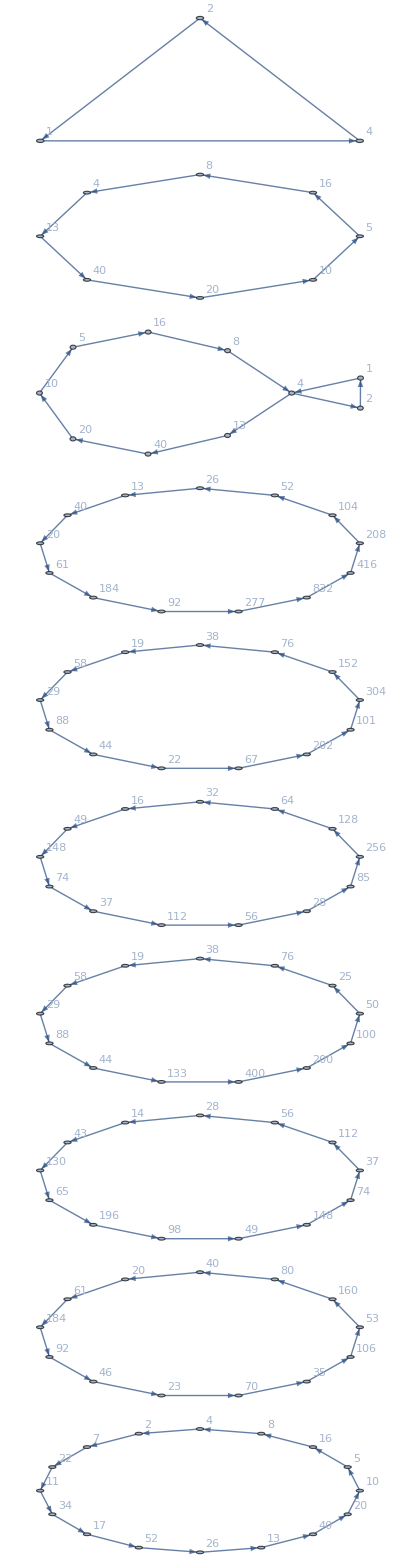

```mathematica
Monitor[Table[
With[{sol=(x/.First[Solve[IntegerToList[k]==x,x]])},
Graph[Sort[DeleteDuplicates[ApplyOpsGraph[Factor[(x/.First[Solve[IntegerToList[k]==x,x]])],Rest[IntegerDigits[k+2,2]]]]], VertexLabels->"Name"]
],{k,IntegerCycles[100000]}],k]//DeleteDuplicates//TableForm
```

## Stability of the form

```mathematica
3^n x*Sum[3^(i-1)*2^Indexed[a,i],{i,1,n}]/2^m
```

2^-m 3^n x ∑_(i=1)^n 2^ai 3^(-1+i)

```mathematica
MyDiv[3^n x*Sum[3^(i-1)*2^Indexed[a,i],{i,1,n}]/2^m]//Factor
```

2^(-1-m) 3^n x ∑_(i=1)^n 2^ai 3^(-1+i)

```mathematica
Mult[3^n x*Sum[3^(i-1)*2^Indexed[a,i],{i,1,n}]/2^m]//Factor
```

2^-m (2^m+3^(1+n) x ∑_(i=1)^n 2^ai 3^(-1+i))